FittedModel[0.]

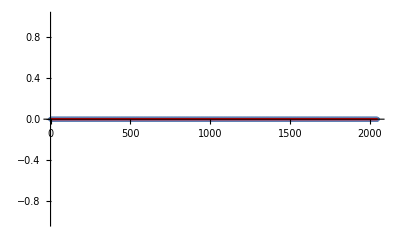

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0.\ ComplexInfinity encountered.

Indeterminate

```mathematica
SetOptions[EvaluationNotebook[],CellContext->Notebook]
name := "gre"
data :=Import[StringJoin["/Users/greg/Documents/School/Science_Research/workspace/ODRA-with-Enums/greg/queries/benchmarks-",name,".csv"], "Table", {"FieldSeparators" -> ";"}][[All,{1,3}]]
nlm = NonlinearModelFit[data, a+b*x,{a,b},x]
Show[ListPlot[data],Plot[nlm[x],{x,0,2048},PlotStyle->Red]]
nlm["RSquared"]
```